# Extensions

In this guide we discuss several extensions of the simple case of a massless scalar in AdS_5.

We first show how to compute the eigenfunctions in addition to the modes.

The package is directly applicable to coupled equations, perturbations on top of a numerical background, and equations of higher order in the frequency. We discuss all these generalizations below.

This loads the package:

```mathematica
Needs["QNMspectral`"]
```

### Computing and viewing eigenfunctions

We continue with the equation for a massless scalar perturbation in Schwarzschild AdS_5 used in the basic tutorial.

```mathematica
eqϕ = (-3-4 q^2 u^2-9 u^4+6 ⅈ u λ) δϕfin[u]+u (3-7 u^4+4 ⅈ u λ) δϕfin'[u]+(u^2-u^6) δϕfin''[u];
```

To compute the quasinormal mode functions ϕ_n(z) along with their frequencies ω_n, we simply set the option Eigenfunctions to True.

```mathematica
modes=GetAccurateModes[eqϕ/.q->0,{60,0},{120,0},Eigenfunctions->True];//AbsoluteTiming
```

{0.097495,Null}

Now modes contains both the functions and the frequencies. We can still use the same functions to show the frequencies:

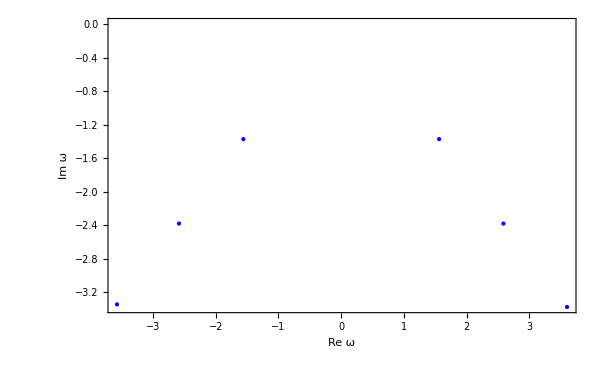
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1.5597258 | -1.3733379
2 | ± 2.58476 | -2.3818
3 | ± 3.6 | -3.
4 | ± 3.6 | -3.4}

```mathematica
ShowModes[modes]
```

Now we can also look at the eigenfunctions:

```mathematica
PlotEigenfunctions[modes,FrameLabel->{"u","u^4δϕ(u)"}]
```

-Graphics-

By default all modes are plotted, but this can be changed with the option NModes. For more details see PlotEigenfunctions.

### Coupled equations

For simplicity we consider a trivial case of two 'coupled' equations: we simply take the massless scalar equation from above at two different values of the momentum:

```mathematica
eqϕCoupled = {eqϕ/.q->0,eqϕ/.q->1/.δϕfin->δψ};
```

We stress that these are of course not actually coupled and it would be very unwise to compute them together instead of separately. For illustrational purposes this is perfectly fine however.

Practically the computation is done exactly the same way as for the uncoupled case:

```mathematica
modesCoupled=GetAccurateModes[eqϕCoupled,{60,0},{120,0}];//AbsoluteTiming
```

{0.216297,Null}

If your computer is slow enough (otherwise try increasing the precision) you will see a temporary message saying that because we are dealing with 2 coupled equations, we have to use a grid of twice the size. For more details on how this works, see the guide on the methods. This temporary message can get annoying when computing a large number of modes at once, to turn it off one can set $QNMQuiet to True.

Now we get the spectra of both q=0 and q=1:

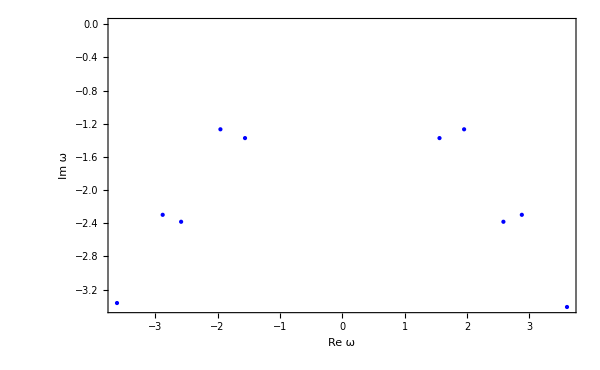
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1.954330883 | -1.26732726
2 | ± 1.559725795 | -1.37333787
3 | ± 2.8803 | -2.298
4 | ± 2.58476 | -2.3818
5 | ± 3.6 | -3.
6 | ± 3.6 | -3.}

```mathematica
ShowModes[modesCoupled]
```

It is perhaps instructive to look at the eigenfunctions in this case:

```mathematica
modesCoupledEfs=GetAccurateModes[eqϕCoupled,{60,0},{120,0},Eigenfunctions->True];//AbsoluteTiming
```

{0.289117,Null}

Now we plot the eigenfunctions corresponding to the first mode, with the q=0 one on the left and the q=1 on the right:

```mathematica
{PlotEigenfunctions[modesCoupledEfs,NModes->2,FrameLabel->{"u","δϕfin(u)"}],
PlotEigenfunctions[modesCoupledEfs,NModes->2,FunctionNumber->2,FrameLabel->{"u","δψ(u)"}]}
```

-Graphics-

The q=0 eigenfunction vanishes, as the first mode corresponds to the q=1 case, as you can easily check from the decoupled equations.

Note that the functions are ordered lexicographically, so to see that δψ corresponds to the second function,

```mathematica
Sort[{δψ[u],δϕfin[u]}]
```

{δϕfin[u],δψ[u]}

Finally note that although we set NModes to 2, we only see one eigenfunction. This is because they come in conjugate pairs. By default only imaginary parts which are positive near the boundary are plotted, for more details see PlotEigenfunctions.

### Numerical background

Again we use the same massless scalar in Schwarzschild AdS_5 as an example to keep things simple.

```mathematica
eqϕf =δϕfin[u] (2 π u (-2 π q^2 u+3 ⅈ λ)-3 f[u]+3 u f'[u])+4 ⅈ π u^2 λ δϕfin'[u]+u^2 f'[u] δϕfin'[u]+f[u] (3 u δϕfin'[u]+u^2 δϕfin''[u]);
```

Here we pretend that the (rescaled) blackening factor f is not known analytically. Let's create a numerical approximation:

```mathematica
fAnalytic[u_]:=1-u^4
fInterp=Interpolation[{#,fAnalytic[#]}&/@Range[0,1,1./50]];
```

This is the easiest way, knowing the values on a set of points, which doesn't need to have any relation to the grid used in the quasinormal mode computation, we let Mathematica create an interpolating function, and we can use this directly:

```mathematica
modesInterp=GetModes[eqϕf/.q->1/.f->fInterp,{50,0}];
```

This works fine, however there is another option, when more precision is needed and the background happens to be known on a (sufficiently large) spectral grid as well.

First we create this data:

```mathematica
grid=Rescale[Cos[π/50 N@Range[0,50]],{-1,1},{0,1}];
fOnGrid=fAnalytic/@grid;
```

Here grid is the same grid as is used internally by GetModes, for N = 50, and fOnGrid is a list of the values of the blackening function on this grid.

```mathematica
modesOnGrid=GetModes[eqϕf/.q->1,{50,0},NumericalBackground->{f->fOnGrid}];//AbsoluteTiming
```

{0.014673,Null}

Note that we only have to specify f, not its derivatives.

In this very simple case the interpolating function is very accurate, but still we can see that it is more accurate to specify the values directly on the grid:

```mathematica
modesAnalytic=GetAccurateModes[eqϕf/.f->fAnalytic/.q->1,{150,0},{100,0}];
```

```mathematica
modesInterp[[1]]
modesOnGrid[[1]]
modesAnalytic[[1]]
```

1.19954-0.318407 ⅈ

-1.19954-0.318402 ⅈ

1.199541729-0.318402202 ⅈ

Here the difference is only visible in the 6th decimal of the imaginary part, but for a nontrivial case one can expect a bigger difference.

### Higher powers of the frequency

For this demonstration we need to move away from the simplest case, and we consider the sound channel in Schwarzschild AdS_5:

```mathematica
soundAdS5=(4 q^4 u^2 (-3+u^4)+9 λ^2 (1+3 u^4-2 ⅈ u λ)+q^2 (-9+u^8+18 ⅈ u λ+10 ⅈ u^5 λ+12 u^2 λ^2)) Z2[u]+u (3 λ^2 (-3+7 u^4-4 ⅈ u λ)-q^2 (-9+16 u^4+u^8-12 ⅈ u λ+4 ⅈ u^5 λ)) Z2'[u]+u^2 (-1+u^4) (q^2 (-3+u^4)+3 λ^2) Z2''[u];
```

Note that this is of third order in the frequency λ = ω/2π T (this can arise from a second order equation because we have to decouple the gauge-invariant functions from the gauge-dependent ones).

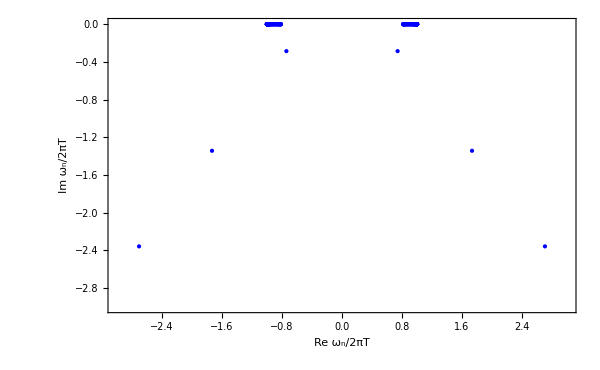
{-Graphics-,n | Re ω_n/2πT | Im ω_n/2πT
1 | ± 1. | 9.×10^-17
2 | ± 0.7414299655 | -0.2862800072
3 | ± 1.7335111 | -1.343008
4 | ± 2.706 | -2.36}

```mathematica
(soundModesAdS5=GetAccurateModes[soundAdS5/.q->1,{100,0},{150,0}])//ShowModes[#,PlotRange->{{-3,3},{-3,0}},Name->"ω_n/2πT"]&
```

Again a message is printed temporarily to warn you that because the frequency occurs to power 3, we have to work with matrices which are 3 times as large.

In general, if we have N_eq coupled equations and the highest power of the frequency is p, working with a base grid size of (N+1), the total grid size will be N_tot=N_eq p(N+1).

Further, the result can be compared to the table on page 26 of 0506184 (our 2nd mode is the sound mode, shown in the text above the table, modes 3 and 4 are their modes 1 and 2 in the table).

Note all the modes near λ = q = 1, these are incorrect modes which are not filtered out by GetAccurateModes. Their origin comes from the asymptotics of the equation:

```mathematica
Series[soundAdS5,{u,0,3}]//Normal//Simplify
```

-3/2 (q^2-λ^2) (2 (3+4 q^2 u^2-6 ⅈ u λ) Z2[0]+u^2 (8 q^2 u Z2'[0]-5 Z2''[0]-2 ⅈ λ (10 Z2'[0]+7 u Z2''[0])-4 u Z2^(3)[0]))

Note that up to third order in u near the boundary, the equation is satisfied if λ = q. One can compute and inspect the eigenfunctions to determine that these are not sensible solutions.

This serves as a warning that GetAccurateModes is not foolproof. We have to filter out these modes ourselves (in this case it could be done by checking if the corresponding functions satisfy the boundary conditions and are smooth).

To get an accuracy comparable to the table in the reference, we have to use a higher precision, which unfortunately slows down the computation much more than increasing the grid size:

{293.015,Null}

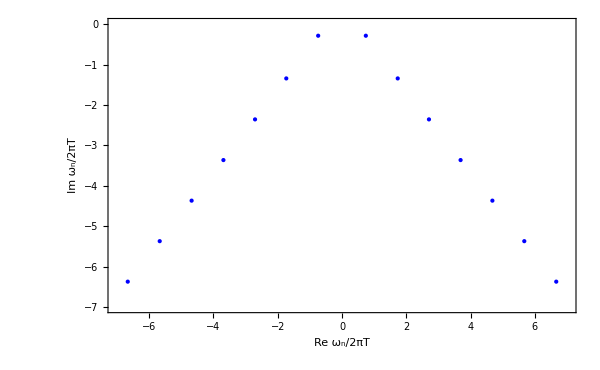
{-Graphics-,n | Re ω_n/2πT | Im ω_n/2πT
1 | ± 0.74143 | -0.28628
2 | ± 1.733511 | -1.343008
3 | ± 2.70554 | -2.357062
4 | ± 3.689391 | -3.363863
5 | ± 4.678735 | -4.367981
6 | ± 5.671091 | -5.370784
7 | ± 6.665291 | -6.372835
8 | ± 7.66071 | -7.3744
9 | ± 8.66 | -8.4
10 | ± 8.66 | -8.4}

```mathematica
soundModesAdS5accurate=GetAccurateModes[soundAdS5/.q->1,{80},{60}]//Select[#,Im[#]<-.1&]&;//AbsoluteTiming
soundModesAdS5accurate//ShowModes[#,PlotRange->{{-1,1}7,{-7,0}},Name->"ω_n/2πT",Precision->7]&
```

RELATED TUTORIALS

Introduction

Simple Example

Method